```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching ""Global`*"".

```mathematica
Mean[PoissonDistribution[x]]
```

x

```mathematica
Variance[PoissonDistribution[x]]
```

x

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x]*x,{x,-∞,∞}]
```

ConditionalExpression[μ/(√(1/σ^2) σ),Re[1/σ^2]≥0]

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x]*x^2,{x,-∞,∞}]
```

ConditionalExpression[(μ^2+σ^2)/(√(1/σ^2) σ),Re[1/σ^2]≥0]

```mathematica
Integrate[PDF[NormalDistribution[μ,σ],x]*x^3,{x,-∞,∞}]
```

ConditionalExpression[(μ (μ^2+3 σ^2))/(√(1/σ^2) σ),Re[1/σ^2]≥0]

```mathematica
Sum[PDF[BinomialDistribution[n,p],k]*k,{k,0,n}]
```

Piecewise[{{n p, n>1}, {-(n (1-p)^n p)/(-1+p), n==1}, {0, True}}]

```mathematica
Sum[PDF[BinomialDistribution[n,p],k]*k^2,{k,0,n}]
```

Piecewise[{{-(n (1-p)^n p)/(-1+p), n==1}, {p (n-n p+n^2 p), n>1}, {0, True}}]

```mathematica
Sum[PDF[BinomialDistribution[n,p],k]*k^3,{k,0,n}]
```

Piecewise[{{-(n (1-p)^n p)/(-1+p), n==1}, {p (n-3 n p+3 n^2 p+2 n p^2-3 n^2 p^2+n^3 p^2), n>1}, {0, True}}]

```mathematica
data1=Table[data=RandomVariate[MaxwellDistribution[Sqrt[Pi/2]],2000];Mean[data],{k,5000}];
```

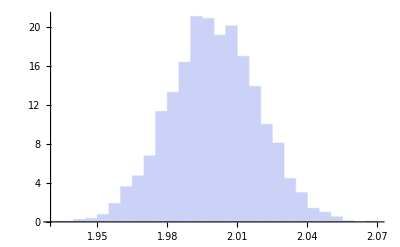

```mathematica
Histogram[data1,20,"ProbabilityDensity"]
```

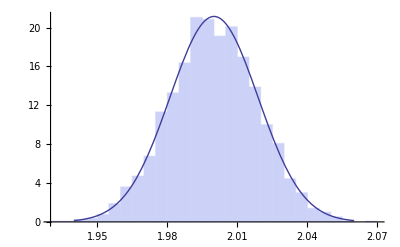

```mathematica
Show[
Histogram[data1,20,"ProbabilityDensity"],
Plot[
PDF[NormalDistribution[2,Sqrt[(3*Pi-8)/(2*2000)]],x],{x,1.94,2.06},PlotRange->All]
]
```

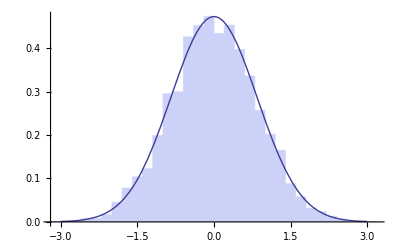

```mathematica
Show[
Histogram[Sqrt[2000]*(data1-2),20,"ProbabilityDensity"],
Plot[
PDF[NormalDistribution[0,Sqrt[(3*Pi-8)/2]],x],{x,-3,3},PlotRange->All]
]
```

```mathematica
data1=Table[data=RandomVariate[PoissonDistribution[1],2000];Mean[data],{k,5000}];
```

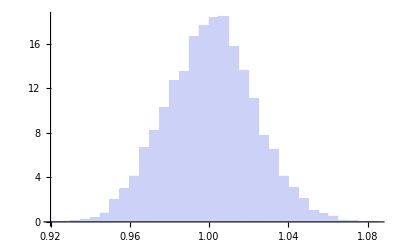

```mathematica
Histogram[data1,40,"ProbabilityDensity"]
```

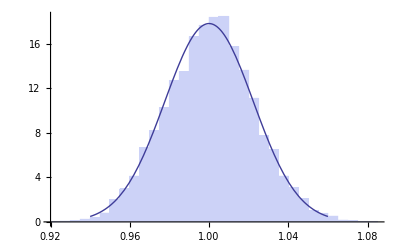

```mathematica
Show[
Histogram[data1,40,"ProbabilityDensity"],
Plot[
PDF[NormalDistribution[1,Sqrt[1/2000]],x],{x,0.94,1.06},PlotRange->All]
]
```

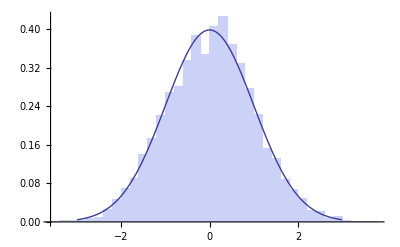

```mathematica
Show[
Histogram[Sqrt[2000]*(data1-1),40,"ProbabilityDensity"],
Plot[
PDF[NormalDistribution[0,1],x],{x,-3,3},PlotRange->All]
]
```

```mathematica
piEst = Table[
data=
Table[{RandomReal[{-1,1}],RandomReal[{-1,1}]},{50000}];
For[i=1;m=0,i<50000,i++,
If[Sqrt[data[[i,1]]^2+data[[i,2]]^2]<1,m++]
];
n=N[m*4/50000],{j,100}]
```

{3.1428,3.13008,3.1372,3.14008,3.13544,3.13592,3.13056,3.1444,3.14728,3.13768,3.13264,3.13264,3.15168,3.14888,3.13904,3.1356,3.13536,3.13696,3.13344,3.13656,3.13568,3.15528,3.14144,3.14888,3.14136,3.14256,3.138,3.15128,3.1368,3.1388,3.14056,3.14704,3.1476,3.1396,3.15648,3.14416,3.13992,3.14016,3.13288,3.14016,3.14944,3.14416,3.13984,3.14912,3.14736,3.1424,3.14816,3.1428,3.14064,3.1432,3.14376,3.14256,3.148,3.14584,3.13672,3.13728,3.1452,3.13296,3.14896,3.14688,3.14264,3.134,3.14064,3.14304,3.13656,3.13168,3.15072,3.14184,3.1504,3.15616,3.1408,3.146,3.1464,3.1444,3.15008,3.15552,3.15112,3.13928,3.14984,3.1468,3.13232,3.13848,3.13344,3.13368,3.14744,3.14088,3.15864,3.15024,3.13632,3.13704,3.13264,3.13632,3.1388,3.14984,3.14056,3.15056,3.14016,3.13584,3.15024,3.14784}

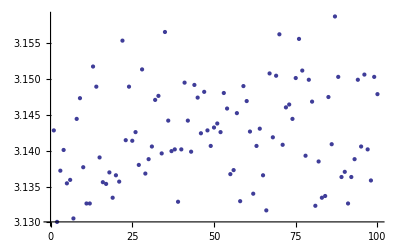

```mathematica
ListPlot[piEst]
```

```mathematica
Mean[piEst]
```

3.14227

```mathematica
Variance[piEst]
```

0.0000434652

```mathematica
P= Table[0,{i,3000},{j,3000}];
```

```mathematica
For[i=1,i≤3000,i++,
For[j=i,j≤3000,j++,
P[[i,j]]=RandomVariate[NormalDistribution[0.5,1]];
P[[j,i]]=P[[i,j]];
]]
```

```mathematica
eign=Eigenvalues[P];
```

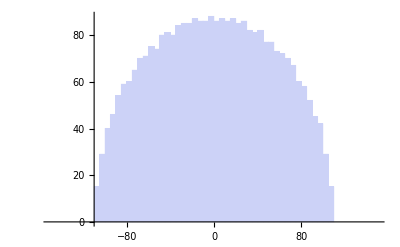

```mathematica
Histogram[eign,{-150,150,5}]
```

```mathematica
eign2=Table[
{(t-16)*10,BinCounts[eign,{-150,150,10}][[t]]}
,{t,1,30}]
```

{{-150,0},{-140,0},{-130,0},{-120,0},{-110,44},{-100,86},{-90,113},{-80,125},{-70,141},{-60,149},{-50,161},{-40,164},{-30,170},{-20,173},{-10,174},{0,173},{10,173},{20,171},{30,163},{40,159},{50,150},{60,142},{70,127},{80,110},{90,87},{100,44},{110,0},{120,0},{130,0},{140,0}}

```mathematica
For[m=1;sum=0,m≤30,m++,sum=sum+10*BinCounts[eign,{-150,150,10}][[m]]
]
```

```mathematica
sum
```

29990

```mathematica
eign3=eign2;
```

```mathematica
eign3[[All,2]]=N[eign2[[All,2]]/29990]
```

{0.,0.,0.,0.,0.00146716,0.00286762,0.00376792,0.00416806,0.00470157,0.00496832,0.00536846,0.00546849,0.00566856,0.00576859,0.00580193,0.00576859,0.00576859,0.0057019,0.00543515,0.00530177,0.00500167,0.00473491,0.00423474,0.00366789,0.00290097,0.00146716,0.,0.,0.,0.}

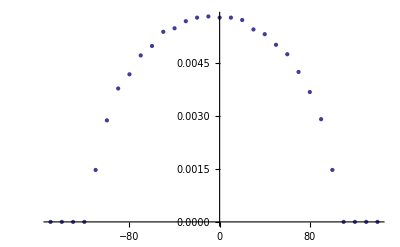

```mathematica
ListPlot[eign3]
```

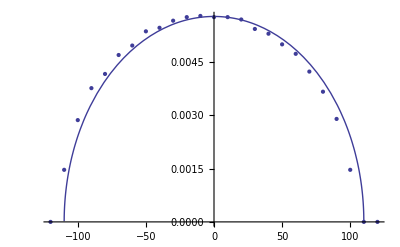

```mathematica
Show[
Plot[2/(Pi*110^2)*Sqrt[110^2-x^2],{x,-120,120}],
ListPlot[eign3]
]
```

```mathematica
Mean[eign3[[All,2]]]
```

0.00333333

```mathematica
Variance[eign3[[All,2]]]
```

5.4932×10^-6